## NLL Angularities

### Load Formulae

```mathematica
αsCR=0.117998;(*0.1184;*)
mZ=91.19;
```

```mathematica
L[C_,R_,β_]:=Log[(2^(β-1)R^β)/C];
α[kt_]:=(1/αsCR+23/(6π)Log[kt/mZ]+116/(92π)Log[1+23/(6π)αsCR Log[kt/mZ]])^-1;
β0=11/(4π)-5/(6π);
β1=153/(24 π^2)-75/(24 π^2)-20/(24 π^2);
K=(67/6-π^2/2)-25/9;
Bg[NF_]:=-(33-2NF)/36;
λ[L_,kt_]:=α[kt]*β0*L;
r[L_,kt_,β_]:=L/(2π β0 λ[L,kt](β-1))((1-2λ[L,kt])Log[1-2λ[L,kt]]-(β-2λ[L,kt])Log[1-(2λ[L,kt])/β])+1/(β-1)(K/(4 π^2 β0^2)(β Log[1-(2λ[L,kt])/β]-Log[1-2λ[L,kt]])+β1/(2π β0^3)(Log[1-2λ[L,kt]]^2/2-β/2 Log[1-(2λ[L,kt])/β]^2+Log[1-2λ[L,kt]]-β Log[1-(2λ[L,kt])/β]));
T[L_,kt_]:=-1/(π β0)Log[1-2λ[L,kt]];
dr[L_,kt_,β_]:=1/(β-1)(T[L,kt]-T[L/β,kt]);
fq[L_,kt_,β_]:=ⅇ^(-EulerGamma 4/3 dr[L,kt,β])/Gamma[1+4/3 dr[L,kt,β]] ⅇ^(-4/3(r[L,kt,β]-3/4 T[L/β,kt]));
fg[L_,kt_,β_,NF_]:=ⅇ^(-EulerGamma 3 dr[L,kt,β])/Gamma[1+3 dr[L,kt,β]] ⅇ^(-3(r[L,kt,β]+Bg[NF] T[L/β,kt]));
dsigmaquark[C1_,R_,kt_,β_,δ_]:=(fq[L[C1+δ,R,β],kt,β]-fq[L[C1,R,β],kt,β])/δ;
dsigmagluon[C1_,R_,kt_,β_,NF_,δ_]:=(fg[L[C1+δ,R,β],kt,β,NF]-fg[L[C1,R,β],kt,β,NF])/δ;
Fshape[ϵ_,Ω_]:=(4ϵ)/Ω^2 ⅇ^(-(2ϵ)/Ω);
dsigmaquarkSHAPE[C1_,R_,kt_,β_,δ_,Ω_]:=NIntegrate[Fshape[ϵ,Ω]dsigmaquark[C1-ϵ/kt-(ϵ/kt)^β,R,kt,β,δ],{ϵ,0,kt}]//Chop;
dsigmagluonSHAPE[C1_,R_,kt_,β_,NF_,δ_,Ω_]:=NIntegrate[Fshape[ϵ,Ω]dsigmagluon[C1-ϵ/kt-(ϵ/kt)^β,R,kt,β,NF,δ],{ϵ,0,kt}]//Chop;
```

```mathematica
(*
Need to normalize distributions appropriately, match to FO, double check formulae
*)
```

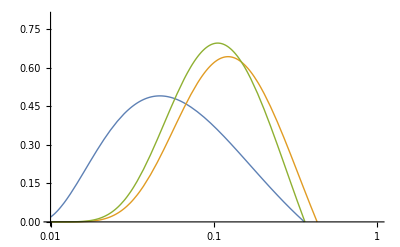

```mathematica
LogLinearPlot[{x dsigmaquark[x,0.8,500,0.5,0.0001],x dsigmagluon[x,0.8,500,0.5,5,0.0001],x dsigmagluon[x,0.8,500,0.5,0,0.0001]},{x,0.01,1},PlotRange->{{0.01,1},{0,0.8}},PlotStyle->Thick]
```

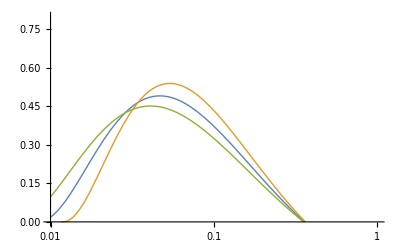

```mathematica
LogLinearPlot[{x dsigmaquark[x,0.8,500,0.5,0.0001],x dsigmaquark[x,0.8,250,0.5,0.0001],x dsigmaquark[x,0.8,1000,0.5,0.0001]},{x,0.01,1},PlotRange->{{0.01,1},{0,0.8}},PlotStyle->Thick]
```

```mathematica
Series[(x-x^β)/(β-1),{β,1,1}]
```

-x Log[x]-1/2 (x Log[x]^2) (β-1)+O[β-1]^2

```mathematica
dsigmaquarkSHAPE[C1_,R_,kt_,β_,δ_,Ω_]:=NIntegrate[Fshape[ϵ,Ω]dsigmaquark[C1-ϵ/kt-(ϵ/kt)^β,R,kt,β,δ],{ϵ,0,kt}]//Chop;
```

```mathematica
Table[{10^(-i/10),10^(-i/10) dsigmaquarkSHAPE[10^(-i/10),1,500,0.5,0.00001,1]},{i,1,20}]
```

{{1/10^(1/10),-0.136869},{1/10^(1/5),-0.0920212},{1/10^(3/10),-0.0349729},{1/10^(2/5),0.0363351},{1/(√10),0.124491},{1/10^(3/5),0.232884},{1/10^(7/10),0.365983+0.00029618 ⅈ},{1/10^(4/5),-0.22354+1.377 ⅈ},{1/10^(9/10),-50.4186-35.8581 ⅈ},{1/10,-3047.66-1273.4 ⅈ},{1/(10 10^(1/10)),-2705.51-2575.6 ⅈ},{1/(10 10^(1/5)),6.10815×10^6+6.45148×10^6 ⅈ},{1/(10 10^(3/10)),8479.4-6707.13 ⅈ},{1/(10 10^(2/5)),46724.5-47894.5 ⅈ},{1/(10 √10),-1050.86+441.036 ⅈ},{1/(10 10^(3/5)),-522.605+40.3025 ⅈ},{1/(10 10^(7/10)),77927.+1.82128×10^6 ⅈ},{1/(10 10^(4/5)),-23.7709+1.81506 ⅈ},{1/(10 10^(9/10)),-6.31775+12.4844 ⅈ},{1/100,-47.9844+62.6341 ⅈ}}